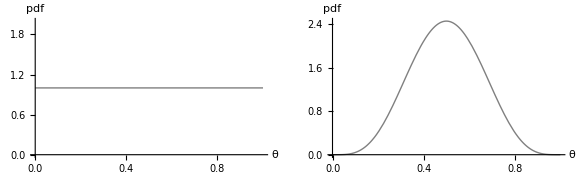

```mathematica
vUniform = Plot[PDF[UniformDistribution[{0,1}],x],{x,0,1},BaseStyle->{FontSize->16},AxesLabel->{"θ","pdf"},PlotStyle->{Gray}];
vFair = Plot[PDF[BetaDistribution[5,5],x],{x,0,1},BaseStyle->{FontSize->16},AxesLabel->{"θ","pdf"},PlotStyle->{Gray}];
Show[GraphicsRow[{vUniform,vFair}],ImageSize->Large]
```